```mathematica
PerBucket=Association[];
Table[PerBucket[allGraphs4[k,"vertexsets"]]={},{k,Keys[allGraphs4]}];
Table[PerBucket[allGraphs4[k,"vertexsets"]]=Append[PerBucket[allGraphs4[k,"vertexsets"]],k],{k,Keys[allGraphs4]}];
Length[PerBucket]
```

15

```mathematica
Product[m,{m,Table[Length[PerBucket[k]],{k,Keys[PerBucket]}]}]
```

2147483648

```mathematica
Table[Log[2,Length[PerBucket[k]]],{k,Keys[PerBucket]}]//Tally//Sort
```

{{0,1},{1,7},{3,6},{6,1}}

```mathematica
{{0,1},{1,4},{4,1}}
```

{{0,1},{1,4},{4,1}}

```mathematica
randoms =Sort[Table[First[RandomSample[PerBucket[k],1]],{k,Keys[PerBucket]}],CompareSymbols[SetsToSymbol2[allGraphs4[#1,"vertexsets"]],SetsToSymbol2[allGraphs4[#2,"vertexsets"]]]&]
```

{13,257,18,16,606,417,63,488,448,72,377,697,546,218,728}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],{k,randoms}]
```

{-Graphics-13,-Graphics-257,-Graphics-18,-Graphics-16,-Graphics-606,-Graphics-417,-Graphics-63,-Graphics-488,-Graphics-448,-Graphics-72,-Graphics-377,-Graphics-697,-Graphics-546,-Graphics-218,-Graphics-728}

```mathematica
PartitionToSymbol4[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["r"<>end]]
```

```mathematica
randomSyms=Sort[Table[PartitionToSymbol4[allGraphs4[k,"vertexsets"]],{k,randoms}],CompareSymbols]
```

{r1x2x3x4,r1x2x34,r1x23x4,r1x24x3,r12x3x4,r13x2x4,r14x2x3,r12x34,r13x24,r14x23,r1x234,r123x4,r124x3,r134x2,r1234}

```mathematica
syms=Sort[Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}],CompareSymbols]
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
randomRep2=Table[PartitionToSymbol4[allGraphs4[k,"vertexsets"]]->Tooltip[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],allGraphs4[k,"compwhy"]],{k,randoms}];
```

```mathematica
randommat=Table[PartitionToSymbol4[allGraphs4[k,"vertexsets"]]==allGraphs4[k,"colofour"],{k,randoms}];TableForm[randommat];
```

```mathematica
randomfullsol=First[Solve[randommat,syms]]
```

{v1x2x3x4→-4 r1234+r124x3+r12x34-r12x3x4+2 r134x2-r13x2x4-r14x2x3+r1x2x3x4,v1x2x34→r1234-r134x2+r1x2x34,v1x23x4→-r123x4-r14x23-r1x234+r1x23x4,v1x24x3→r1234-r124x3-r13x24+r1x24x3,v12x3x4→r1234-r12x34+r12x3x4,v13x2x4→r1234-r134x2+r13x2x4,v14x2x3→2 r1234-r124x3-r134x2+r14x2x3,v12x34→-r1234+r12x34,v13x24→r13x24,v14x23→-r1234+r14x23,v1x234→r1x234,v123x4→r123x4,v124x3→-r1234+r124x3,v134x2→-r1234+r134x2,v1234→r1234}

```mathematica
TableForm[
Table[
Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]]->
{allGraphs4[k,"colofour"]/.randomfullsol/.randomRep2,allGraphs4[k,"colofour"]/.randomfullsol},
{k,allGraphs4AtomKeys}
]
]
```

-Graphics-364→{-4 -Graphics-728+-Graphics-546+-Graphics-488+2 -Graphics-218--Graphics-63--Graphics-606--Graphics-417+-Graphics-13,-4 r1234+r124x3+r12x34-r12x3x4+2 r134x2-r13x2x4-r14x2x3+r1x2x3x4}
-Graphics-365→{-Graphics-728--Graphics-218+-Graphics-257,r1234-r134x2+r1x2x34}
-Graphics-367→{-Graphics-728--Graphics-546--Graphics-448+-Graphics-16,r1234-r124x3-r13x24+r1x24x3}
-Graphics-373→{--Graphics-72--Graphics-697--Graphics-377+-Graphics-18,-r123x4-r14x23-r1x234+r1x23x4}
-Graphics-377→{-Graphics-377,r1x234}
-Graphics-391→{2 -Graphics-728--Graphics-546--Graphics-218+-Graphics-63,2 r1234-r124x3-r134x2+r14x2x3}
-Graphics-400→{--Graphics-728+-Graphics-72,-r1234+r14x23}
-Graphics-445→{-Graphics-728--Graphics-218+-Graphics-417,r1234-r134x2+r13x2x4}
-Graphics-448→{-Graphics-448,r13x24}
-Graphics-473→{--Graphics-728+-Graphics-218,-r1234+r134x2}
-Graphics-607→{-Graphics-728--Graphics-488+-Graphics-606,r1234-r12x34+r12x3x4}
-Graphics-608→{--Graphics-728+-Graphics-488,-r1234+r12x34}
-Graphics-637→{--Graphics-728+-Graphics-546,-r1234+r124x3}
-Graphics-697→{-Graphics-697,r123x4}
-Graphics-728→{-Graphics-728,r1234}

```mathematica
{{-Graphics-14->{--Graphics-2--Graphics-22--Graphics-16+-Graphics-0,-r12x4-r14x2-r1x24+r1x2x4}}, {-Graphics-14->{--Graphics-26+-Graphics-2,-r124+r1x24}}, {-Graphics-16->{-Graphics-16,r14x2}}, {-Graphics-22->{-Graphics-22,r12x4}}, {-Graphics-26->{-Graphics-26,r124}}}
```

{-Graphics-14→{--Graphics-2--Graphics-22--Graphics-16+-Graphics-0,-r12x4-r14x2-r1x24+r1x2x4},-Graphics-14→{--Graphics-26+-Graphics-2,-r124+r1x24},-Graphics-16→{-Graphics-16,r14x2},-Graphics-22→{-Graphics-22,r12x4},-Graphics-26→{-Graphics-26,r124}}

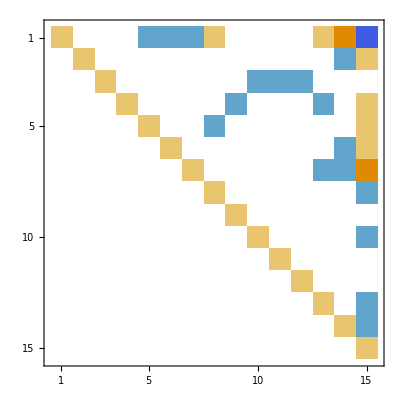

```mathematica
rmat=  Map[
Table[Coefficient[#[[2]],t],{t,randomSyms}]&,
randomfullsol];MatrixPlot[rmat]
```

```mathematica
MatrixRank[rmat]
```

15

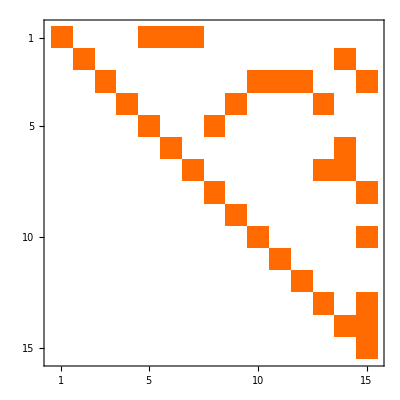

```mathematica
Inverse[rmat]//MatrixPlot
```